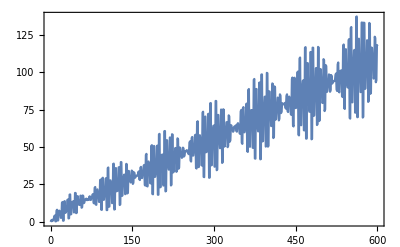

```mathematica
Needs["Quantum`Notation`"];
SetQuantumAliases[];
Remove["Global`*"];
hadamard[j_]:=1/(√2)(|Subscript[0, ĵ]⟩·⟨Subscript[0, ĵ]|+|Subscript[1, ĵ]⟩·⟨Subscript[0, ĵ]|+|Subscript[0, ĵ]⟩·⟨Subscript[1, ĵ]|-|Subscript[1, ĵ]⟩·⟨Subscript[1, ĵ]|);
αA=-51 Degree;
βA=16 Degree;
γA=0 Degree;

αB=0 Degree;
βB=88 Degree;
γB=-16 Degree;

aA=N[Exp[I*αA]*Cos[βA]];
bA=N[-Exp[-I*γA]*Sin[βA]];
cA=N[Exp[I*γA]*Sin[βA]];
dA=N[Exp[-I*αA]*Cos[βA]];

aB=N[Exp[I*αB]*Cos[βB]];
bB=N[-Exp[-I*γB]*Sin[βB]];
cB=N[Exp[I*γB]*Sin[βB]];
dB=N[Exp[-I*αB]*Cos[βB]];
CoinA[j_]:=(aA|Subscript[0, ĵ]⟩·⟨Subscript[0, ĵ]|+bA|Subscript[0, ĵ]⟩·⟨Subscript[1, ĵ]|+cA|Subscript[1, ĵ]⟩·⟨Subscript[0, ĵ]|+dA|Subscript[1, ĵ]⟩·⟨Subscript[1, ĵ]|);
CoinB[j_]:=(aB|Subscript[0, ĵ]⟩·⟨Subscript[0, ĵ]|+bB|Subscript[0, ĵ]⟩·⟨Subscript[1, ĵ]|+cB|Subscript[1, ĵ]⟩·⟨Subscript[0, ĵ]|+dB|Subscript[1, ĵ]⟩·⟨Subscript[1, ĵ]|)
CHEC1=Expand[ CoinA[1]⊗CoinB[2] ];
CHEC2=Expand[ CoinB[1]⊗CoinA[2] ];
steps=600;
gamma=Pi/4;
|weff[0]⟩=|Subscript[0, OverHat[pp]]⟩⊗(Cos[gamma/2]|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+I Sin[gamma/2]|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩);
Do[If [Mod[k,2]==0,
|weff[k]⟩=Expand[ReplaceAll[CHEC1·|weff[k-1]⟩,
{|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[(j+1), OverHat[pp]]⟩,
|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[(j+0), OverHat[pp]]⟩,
|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[(j-0), OverHat[pp]]⟩,
|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[(j-1), OverHat[pp]]⟩}]],

|weff[k]⟩=Expand[ReplaceAll[CHEC2·|weff[k-1]⟩,
{|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[(j+1), OverHat[pp]]⟩,
|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[(j+0), OverHat[pp]]⟩,
|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[(j-0), OverHat[pp]]⟩,
|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[(j-1), OverHat[pp]]⟩}]];],

{k,1,steps,1}
];
X={};
Do[pl=0;pr=0;
Do[ketList=Cases[|weff[s]⟩,x_.*|Subscript[y_, OverHat[1]],Subscript[z_, OverHat[2]],Subscript[j, OverHat[pp]]⟩];
braList=Map[Function[{w},SuperDagger[(w)]],ketList];
productList=
MapThread[Function[{b,k},b·k],{braList,ketList}];
If[j<0 ,pl=pl+s*Apply[Plus,productList],##&[];];
If[j>0 ,pr=pr+s*Apply[Plus,productList],##&[];];,{j,-s,s}]
AppendTo[X,{s,pr-pl}];,{s,0,steps}];
ListPlot[X,Joined->True,PlotRange->All,Frame->True,Axes->False]
```